```mathematica
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"]
```

```mathematica
J[a_,b_,γ_] :=(MatrixExp[-I γ/2 KroneckerProduct[ScaledAntiHermitianMatrix[a],ScaledAntiHermitianMatrix[b]]]);
```

```mathematica
Arg[I a]//ComplexExpand
```

Arg[ⅈ a]

```mathematica
(*Assuming a is positive*)Simplify[Abs[I a],a>0]
```

a

```mathematica
ScaledAntiHermitianMatrix[a]
```

{{ⅈ a,1},{-1,ⅈ a}}

```mathematica
Simplify[Abs[ⅇ^(1/2 ⅈ (-1+a)^2 γ)],{a>0,γ>0}]
```

1

```mathematica
Clear[a]
```

```mathematica
Simplify[Arg[ⅇ^(1/2 ⅈ a)],{a>0,γ>0,a<Pi}]
```

Arg[ⅇ^((ⅈ a)/2)]

```mathematica
(*First,clear any previous definitions for the symbols*)Clear[a,γ];

(*Define your expression*)
expr=Exp[1/2 I (-1+a)^2 γ]+Exp[1/2 I (1+a)^2 γ]+2 Exp[1/2 I (-1+a^2) γ];

(*Use FullSimplify with the assumption that'a' and'γ' are real numbers*)
FullSimplify[expr,Assumptions->{a,γ}∈Reals]
```

ⅇ^(1/2 ⅈ (-1+a)^2 γ)+ⅇ^(1/2 ⅈ (1+a)^2 γ)+2 ⅇ^(1/2 ⅈ (-1+a^2) γ)

```mathematica
FullSimplify[Exp[1/2 I (-1+a)^2 γ]+Exp[1/2 I (1+a)^2 γ]+2 Exp[1/2 I (-1+a^2) γ]]
```

ⅇ^(1/2 ⅈ (-1+a)^2 γ)+ⅇ^(1/2 ⅈ (1+a)^2 γ)+2 ⅇ^(1/2 ⅈ (-1+a^2) γ)

```mathematica
(*Assuming a is positive*)Simplify[Arg[I a],a>0]
```

```mathematica
FullSimplify[FullSimplify[J[a,a,γ]][[1,1]]]
```

1/4 (ⅇ^(1/2 ⅈ (-1+a)^2 γ)+ⅇ^(1/2 ⅈ (1+a)^2 γ)+2 ⅇ^(1/2 ⅈ (-1+a^2) γ))

```mathematica
FullSimplify[J[a,a,γ]]//MatrixForm
```

(1/4 (1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)) | 1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ)) | 1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ)) | 1/4 (-1-ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ))
-1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ)) | 1/4 (1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)) | 1/4 (1+ⅇ^(2 ⅈ a γ)-2 ⅇ^(ⅈ (1+a) γ)) | 1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ))
-1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ)) | 1/4 (1+ⅇ^(2 ⅈ a γ)-2 ⅇ^(ⅈ (1+a) γ)) | 1/4 (1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)) | 1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ))
1/4 (-1-ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)) | -1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ)) | -1/4 ⅈ (-1+ⅇ^(2 ⅈ a γ)) | 1/4 (1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)))

```mathematica
su2[θ1,ϕ1,ζ2]
```

{{ⅇ^(ⅈ θ1) Cos[ζ2],-ⅇ^(ⅈ ϕ1) Sin[ζ2]},{ⅇ^(-ⅈ ϕ1) Sin[ζ2],ⅇ^(-ⅈ θ1) Cos[ζ2]}}

```mathematica
J[a,a,γ]//Arg//ComplexExpand//Simplify//MatrixForm
```

(Arg[1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)] | Arg[ⅈ (-1+ⅇ^(2 ⅈ a γ))] | Arg[ⅈ (-1+ⅇ^(2 ⅈ a γ))] | Arg[-1-ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)]
Arg[-ⅈ (-1+ⅇ^(2 ⅈ a γ))] | Arg[1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)] | Arg[1+ⅇ^(2 ⅈ a γ)-2 ⅇ^(ⅈ (1+a) γ)] | Arg[ⅈ (-1+ⅇ^(2 ⅈ a γ))]
Arg[-ⅈ (-1+ⅇ^(2 ⅈ a γ))] | Arg[1+ⅇ^(2 ⅈ a γ)-2 ⅇ^(ⅈ (1+a) γ)] | Arg[1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)] | Arg[ⅈ (-1+ⅇ^(2 ⅈ a γ))]
Arg[-1-ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)] | Arg[-ⅈ (-1+ⅇ^(2 ⅈ a γ))] | Arg[-ⅈ (-1+ⅇ^(2 ⅈ a γ))] | Arg[1+ⅇ^(2 ⅈ a γ)+2 ⅇ^(ⅈ (1+a) γ)])

```mathematica
finalState =( play[J[0,0,Pi/6],su2[θ1,ϕ1,ζ1],su2[θ2,ϕ2,ζ2]]/.Conjugate-> MyConj);
```

```mathematica
finalState=FullSimplify[Simplify/@ComplexExpand[finalState]];
```

```mathematica
(*Function to find critical points where the first-order conditions are met.*)FindCriticalPoints[ascore_,bscore_,avars_List,bvars_List]:=Module[{gradA,gradB,equations,allvars},(*Calculate the gradient of each player's score w.r.t.their own variables*)
Print["Calculating Grad A"];
gradA=Map[Simplify,Grad[ascore,avars],{2}];
Print["Calculating Grad B"];
gradB=Map[Simplify,Grad[bscore,avars],{2}];
(*Create a system of equations by setting the gradients to zero*)equations=Join[Thread[gradA==0],Thread[gradB==0]];
(*Combine all strategy variables into a single list*)allvars=Join[avars,bvars];
Print["Reducing"];
(*Print[equations];*)
(*Solve the system for the strategy variables*)equations]
(*Function to find and filter for possible Nash Equilibria.It returns a list of {solution,conditions} pairs,excluding those whose conditions are impossible (i.e.,False).*)VerifyNashEquilibria[ascore_,bscore_,avars_List,bvars_List,candidates_List]:=Module[{annotatedSolutions={}},Do[Module[{ascoreNumeric,bscoreNumeric,amax,bmax,isNash,ascoreWithBFixed},(*1. Calculate the scores for both players at the current candidate point.*)ascoreNumeric=ascore/. candidate;
bscoreNumeric=bscore/. candidate;
(*2. Fix player B's variables and find the absolute maximum score player A can achieve.*)(*We use FilterRules to get only player B's rules from the candidate list*)
ascoreWithBFixed=ascore/. FilterRules[candidate,bvars];
Module[{},(*NMaximize returns {value,{vars...}},

so we take the First part.*)amax=First[NMaximize[ascoreWithBFixed,avars]];];

(*3. Fix player A's variables and find the absolute maximum score player B can achieve.*)Module[{bscoreWithAFixed=bscore/. FilterRules[candidate,avars]},bmax=First[NMaximize[bscoreWithAFixed,bvars]];];
(*4. Check for Nash Equilibrium condition.The candidate is a NE if the player's score at that point is the maximum possible score (i.e.,no player has an incentive to deviate).We use a small tolerance for numerical precision.*)
Print[amax,ascoreNumeric,bmax,bscoreNumeric];

isNash=(amax<=ascoreNumeric+1*^-6)&&(bmax<=bscoreNumeric+1*^-6);
If[isNash,Print["Verified NE: ",candidate->{ascoreNumeric,bscoreNumeric}];
AppendTo[annotatedSolutions,{candidate,"Verified with NMaximize",{ascoreNumeric,bscoreNumeric}}]];],{candidate,candidates}];
]
```

```mathematica
aScoresComputed =(alicesScore[finalState]/.Conjugate->MyConj);
```

```mathematica
bScoresComputed =(bobsScore[finalState]/.Conjugate->MyConj);
```

```mathematica
aScoresComputed =FullSimplify[ Simplify/@((aScoresComputed))];
bScoresComputed =FullSimplify[ Simplify/@((bScoresComputed))];
```

```mathematica
aScore0Simp =FullSimplify[ Simplify/@((aScoresComputed//.{a->0}))];
```

```mathematica
bScore0Simp = FullSimplify[ Simplify/@((bScoresComputed//.{a->0}))];
```

```mathematica
Clear[ascore]
Clear[bscore]
```

```mathematica
ascore[amove_,bmove_,game_] :=aScore0Simp/.{θ1->amove[[1]],ϕ1-> amove[[2]],ζ1-> amove[[3]],θ2->bmove[[1]],ϕ2-> bmove[[2]],ζ2-> bmove[[3]]}
bscore[amove_,bmove_,game_] := bScore0Simp/.{θ1->amove[[1]],ϕ1-> amove[[2]],ζ1-> amove[[3]],θ2->bmove[[1]],ϕ2-> bmove[[2]],ζ2-> bmove[[3]]}
```

```mathematica
fastAscore[{0,0},{0,0}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

3

```mathematica
ascore[{a,b,c},{d,e,F},{a}]
```

1/8 (5 (7+Cos[2 b-2 d]) Cos[F]^2 Sin[c]^2+2 Cos[c]^2 ((11+Cos[2 (a+d)]) Cos[F]^2+5 Sin[a-e]^2 Sin[F]^2)+2 (4 Cos[b+e]^2 Sin[c]^2 Sin[F]^2+6 Sin[c]^2 Sin[b+e]^2 Sin[F]^2+Cos[b+e] Sin[2 c] Sin[a+d] Sin[2 F]-5 Cos[b-d] Sin[2 c] Sin[a-e] Sin[2 F]-3 Cos[a+d] Sin[2 c] Sin[b+e] Sin[2 F]))

```mathematica
cf[0,0,0,0]
```

3.

```mathematica
avars = {θ1,ϕ1,ζ1};
bvars = {θ2,ϕ2,ζ2};
criticalPointseq=FindCriticalPoints[aScore0Simp,bScore0Simp,avars,bvars];
```

Calculating Grad A

Calculating Grad B

Reducing

```mathematica
su2[Pi/2,Pi/2,Pi/2]
```

{{0,-ⅈ},{-ⅈ,0}}

```mathematica
criticalPointseq = criticalPointseq//FullSimplify;
```

```mathematica
criticalPointseq//MatrixForm
```

((Cos[θ1+θ2-ϕ1-ϕ2]+5 Cos[θ1-θ2+ϕ1-ϕ2]+2 Cos[θ1+θ2+ϕ1+ϕ2]) Sin[2 ζ1] Sin[2 ζ2]+2 Cos[ζ1]^2 (2 Cos[ζ2]^2 Sin[2 (θ1+θ2)]-5 Sin[ζ2]^2 Sin[2 θ1-2 ϕ2])==0
Sin[2 ζ1] Sin[2 ζ2] (3 Cos[θ1+θ2] Cos[ϕ1+ϕ2]+5 Sin[θ2-ϕ1] Sin[θ1-ϕ2]+Sin[θ1+θ2] Sin[ϕ1+ϕ2])==Sin[ζ1]^2 (5 Cos[ζ2]^2 Sin[2 θ2-2 ϕ1]+2 Sin[ζ2]^2 Sin[2 (ϕ1+ϕ2)])
Cos[ζ1] Cos[ζ2]^2 (-13+2 Cos[2 (θ1+θ2)]-5 Cos[2 θ2-2 ϕ1]) Sin[ζ1]+2 Cos[2 ζ1] Sin[2 ζ2] (5 Cos[θ2-ϕ1] Sin[θ1-ϕ2]+3 Cos[θ1+θ2] Sin[ϕ1+ϕ2])+Sin[2 ζ1] Sin[ζ2]^2 (5 Sin[θ1-ϕ2]^2-6 Sin[ϕ1+ϕ2]^2)==2 Cos[ϕ1+ϕ2] (2 Cos[ϕ1+ϕ2] Sin[2 ζ1] Sin[ζ2]^2+Cos[2 ζ1] Sin[2 ζ2] Sin[θ1+θ2])
(Cos[θ1+θ2-ϕ1-ϕ2]-5 Cos[θ1-θ2+ϕ1-ϕ2]+2 Cos[θ1+θ2+ϕ1+ϕ2]) Sin[2 ζ1] Sin[2 ζ2]+2 Cos[ζ1]^2 (2 Cos[ζ2]^2 Sin[2 (θ1+θ2)]+5 Sin[ζ2]^2 Sin[2 θ1-2 ϕ2])==0
Sin[2 ζ1] Sin[2 ζ2] (5 Cos[θ2-ϕ1] Cos[θ1-ϕ2]-3 Cos[θ1+θ2] Cos[ϕ1+ϕ2]-Sin[θ1+θ2] Sin[ϕ1+ϕ2])+Sin[ζ1]^2 (-5 Cos[ζ2]^2 Sin[2 θ2-2 ϕ1]+2 Sin[ζ2]^2 Sin[2 (ϕ1+ϕ2)])==0
Cos[ζ1] Sin[ζ1] (2 Cos[ζ2]^2 (11+Cos[2 (θ1+θ2)])+(25+5 Cos[2 θ1-2 ϕ2]+2 Cos[2 (ϕ1+ϕ2)]) Sin[ζ2]^2)+Cos[2 ζ1] Sin[2 ζ2] (Sin[θ1+θ2-ϕ1-ϕ2]-5 Sin[θ1-θ2+ϕ1-ϕ2]+2 Sin[θ1+θ2+ϕ1+ϕ2])==5 Cos[ζ2]^2 Sin[2 ζ1] Sin[θ2-ϕ1]^2)

```mathematica
aScore0Simp
```

1/8 (5 Cos[ζ2]^2 (7+Cos[2 θ2-2 ϕ1]) Sin[ζ1]^2+2 Cos[ζ1]^2 (Cos[ζ2]^2 (11+Cos[2 (θ1+θ2)])+5 Sin[ζ2]^2 Sin[θ1-ϕ2]^2)+2 (4 Cos[ϕ1+ϕ2]^2 Sin[ζ1]^2 Sin[ζ2]^2+Cos[ϕ1+ϕ2] Sin[2 ζ1] Sin[2 ζ2] Sin[θ1+θ2]-5 Cos[θ2-ϕ1] Sin[2 ζ1] Sin[2 ζ2] Sin[θ1-ϕ2]-3 Cos[θ1+θ2] Sin[2 ζ1] Sin[2 ζ2] Sin[ϕ1+ϕ2]+6 Sin[ζ1]^2 Sin[ζ2]^2 Sin[ϕ1+ϕ2]^2))

```mathematica
aScore0Simp/.FindRoot[criticalPointseq,{{θ1,0},{ϕ1,0},{ζ1,0},{θ2,Pi/2},{ϕ2,Pi/2},{ζ2,Pi/2}}]
```

1.25

```mathematica
specGamma=specGamma//Reduce//FullSimplify
```

$Aborted

```mathematica
specGamma = criticalPointseq/.γ->Pi/2//Simplify;
```

```mathematica
Solve[specGamma]
```

$Aborted

```mathematica
γ=Pi/4;
gridRes = 2Pi/3;
cps=Flatten[Table[FindRoot[criticalPointseq,{{θ1,t1,0,Pi},{ϕ1,p1,0,2*Pi},{θ2,t2,0,2*Pi},{ϕ2,p2,0,2*Pi}}]//Quiet,{t2,0,2Pi,gridRes},{p1,0,2Pi,gridRes},{p2,0,2Pi,gridRes},{t1,0,2Pi,gridRes}],3];
```

FindRoot::nlnum: The function value {0.+8. Sin[2. ζ1] Sin[2. ζ2],0.+3. Sin[2. ζ1] Sin[2. ζ2],0.-16. Cos[ζ1] Cos[ζ2]^2 Sin[ζ1]-2. (0.+2. Sin[2. ζ1] Sin[ζ2]^2),0.-2. Sin[2. ζ1] Sin[2. ζ2],0.+2. Sin[2. ζ1] Sin[2. ζ2],0.+Cos[ζ1] Sin[ζ1] (24. Cos[ζ2]^2+32. Sin[ζ2]^2)} is not a list of numbers with dimensions {6} at {θ1,ϕ1,θ2,ϕ2} = {0.,0.,0.,0.}.

FindRoot::nlnum: The function value {2. Cos[ζ1]^2 (-1.73205 Cos[ζ2]^2+4.33013 Sin[ζ2]^2)-4. Sin[2. ζ1] Sin[2. ζ2],0.-1.5 Sin[2. ζ1] Sin[2. ζ2],«1»,«1»+«1»,0.-1. Sin[2. ζ1] Sin[2. ζ2],0.+Cos[ζ1] Sin[ζ1] (21. Cos[ζ2]^2+24.5 Sin[ζ2]^2)-1.73205 Cos[2. ζ1] Sin[2. ζ2]} is not a list of numbers with dimensions {6} at {θ1,ϕ1,θ2,ϕ2} = {2.0944,0.,0.,0.}.

FindRoot::nlnum: The function value {2. Cos[ζ1]^2 (1.73205 Cos[ζ2]^2-4.33013 Sin[ζ2]^2)-4. Sin[2. ζ1] Sin[2. ζ2],0.-1.5 Sin[2. ζ1] Sin[2. ζ2],«1»,«1»+«1»,0.-1. Sin[2. ζ1] Sin[2. ζ2],0.+Cos[ζ1] Sin[ζ1] (21. Cos[ζ2]^2+24.5 Sin[ζ2]^2)+1.73205 Cos[2. ζ1] Sin[2. ζ2]} is not a list of numbers with dimensions {6} at {θ1,ϕ1,θ2,ϕ2} = {4.18879,0.,0.,0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::srect: Value t1 in search specification {θ1,t1,0,2 π} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

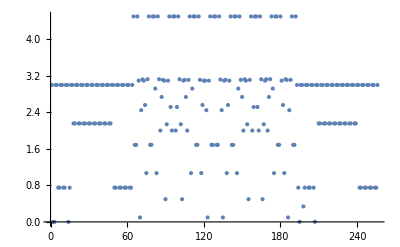

```mathematica
ListPlot[Table[aScore0Simp/.cp,{cp,cps}]]
```

```mathematica
cp//Length
```

```mathematica
cp[[;;3]]
```

{{θ1→0.,ϕ1→0.,θ2→0.,ϕ2→0.},{θ1→1.5708,ϕ1→0.,θ2→0.,ϕ2→0.},{θ1→4.71239,ϕ1→0.,θ2→0.,ϕ2→0.}}

```mathematica
Table[{(su2[θ1,ϕ1]/.ne[[1]])//Chop//MatrixForm,(su2[θ2,ϕ2]/.ne[[1]])//Chop//MatrixForm,ne[[2;;]]},{ne , VerifyNashEquilibria[aScore0Simp,bScore0Simp,{θ1,ϕ1},{θ2,ϕ2},cps]}]
```

3.3.3.3.

Verified NE: {θ1→0.,ϕ1→0.,θ2→0.,ϕ2→0.}→{3.,3.}

3.1.12482×10^-325.5.

3.1.01234×10^-315.5.

3.3.3.3.

Verified NE: {θ1→6.28319,ϕ1→0.,θ2→0.,ϕ2→0.}→{3.,3.}

3.3.3.3.

Verified NE: {θ1→0.,ϕ1→0.,θ2→0.,ϕ2→2.0944}→{3.,3.}

3.0.754.64864.5

3.0.754.64864.5

3.3.3.3.

Verified NE: {θ1→6.28319,ϕ1→0.,θ2→0.,ϕ2→2.0944}→{3.,3.}

3.3.3.3.

Verified NE: {θ1→0.,ϕ1→0.,θ2→0.,ϕ2→4.18879}→{3.,3.}

3.0.754.64864.5

3.0.754.64864.5

3.3.3.3.

Verified NE: {θ1→6.28319,ϕ1→0.,θ2→0.,ϕ2→4.18879}→{3.,3.}

```mathematica
plt
```

-Graphics3D-

```mathematica
Solve[Reduce[su2[θ1,ϕ1,ζ1]=={{0,-1},{1,0}},{θ1,ϕ1,ζ1}]//Simplify,{θ1,ϕ1,ζ1}]
```

{{θ1→ConditionalExpression[π/2, ],ϕ1→ConditionalExpression[π/2, ],ζ1→ConditionalExpression[π, ]}}

```mathematica
{su2[θ1,ϕ1,ζ1]//MatrixForm,su2[θ2,ϕ2,ζ2]//MatrixForm}/.{θ1->0.,ϕ1->0.,ζ1->6.283185307179586,θ2->Pi/2,ϕ2->Pi/2,ζ2->Pi}//Chop
```

{(-1. | 0
0 | -1.),(0 | -1
1 | 0)}

```mathematica
res = play[J[0,0,0],su2[0,0,2Pi],su2[Pi/2,Pi/2,Pi]]
alicesScore[res]
bobsScore[res]
```

{0,-1,0,0}

0

5

```mathematica
criticalPoints = FullSimplify[criticalPoints];
nashEquilibria=VerifyNashEquilibria[aScore0Simp,bScore0Simp,{θ1,ϕ1,ζ1},{θ2,ϕ2,ζ2},criticalPoints]//FullSimplify;
```

```mathematica
nashEquilibria
```

VerifyNashEquilibria[1/16 (-2 Cos[ζ2/2]^2 Sin[ζ1/2]^2 (-23+7 Cos[2 θ1]+10 Cos[2 ϕ1] Sin[θ1]^2)+8 Cos[ζ1/2]^2 (3+3 Cos[ζ2]+Sin[ζ2/2]^2 (4 Cos[θ2]^2+5 Cos[ϕ2]^2 Sin[θ2]^2))-4 Sin[ζ2] (Sin[ζ1] (2 Cos[θ1] Cos[θ2]+√2 Sin[θ1] Sin[θ2] (2 Cos[ϕ2] Sin[ϕ1]-3 Cos[ϕ1] Sin[ϕ2]))+Sin[ζ1/2]^2 Sin[θ1] (5 Cos[θ2] Sin[θ1] Sin[2 ϕ1]+2 √2 Cos[θ1] Sin[θ2] (Cos[ϕ1] Cos[ϕ2]+4 Sin[ϕ1] Sin[ϕ2])))+4 Sin[ζ2/2]^2 (Sin[ζ1/2]^2 Sin[θ1]^2 (5 Cos[θ2]^2 (3+Cos[2 ϕ1])-2 (-3+Cos[2 (ϕ1+ϕ2)]) Sin[θ2]^2)-3 √2 Cos[ϕ2] Sin[ζ1/2]^2 Sin[2 θ1] Sin[2 θ2] Sin[ϕ1]+√2 Sin[ζ1] Sin[θ1] (8 Cos[θ2] Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[2 θ2] Sin[ϕ1] Sin[ϕ2])+2 Cos[θ1]^2 Sin[ζ1/2]^2 (6 Cos[θ2]^2+5 Sin[θ2]^2 Sin[ϕ2]^2)+Cos[θ1] Sin[θ2] (8 √2 Cos[θ2] Cos[ϕ1] Sin[ζ1/2]^2 Sin[θ1] Sin[ϕ2]+5 Sin[ζ1] Sin[θ2] Sin[2 ϕ2]))),1/4 (2 Cos[ζ2/2]^2 Sin[ζ1/2]^2 (4 Cos[θ1]^2+5 Cos[ϕ1]^2 Sin[θ1]^2)+Cos[ζ1/2]^2 (6+6 Cos[ζ2]+Sin[ζ2/2]^2 (8 Cos[θ2]^2-5 Cos[2 ϕ2] Sin[θ2]^2))+Sin[ζ2] (Sin[ζ1] (-2 Cos[θ1] Cos[θ2]+√2 Sin[θ1] Sin[θ2] (3 Cos[ϕ2] Sin[ϕ1]-2 Cos[ϕ1] Sin[ϕ2]))+Sin[ζ1/2]^2 (5 Cos[θ2] Sin[θ1]^2 Sin[2 ϕ1]+√2 Sin[2 θ1] Sin[θ2] (4 Cos[ϕ1] Cos[ϕ2]+Sin[ϕ1] Sin[ϕ2])))+1/2 Sin[ζ2/2]^2 (2 Sin[ζ1/2]^2 ((5 Cos[θ1]^2 (3+Cos[2 ϕ2])-2 (-3+Cos[2 (ϕ1+ϕ2)]) Sin[θ1]^2) Sin[θ2]^2+8 √2 Cos[θ1] Cos[θ2] Cos[ϕ2] Sin[θ1] Sin[θ2] Sin[ϕ1]+2 Cos[θ2]^2 (6 Cos[θ1]^2+5 Sin[θ1]^2 Sin[ϕ1]^2)-3 √2 Cos[ϕ1] Sin[2 θ1] Sin[2 θ2] Sin[ϕ2])+Sin[θ2] (-4 √2 Cos[θ2] Sin[ζ1] Sin[θ1] (Cos[ϕ1] Cos[ϕ2]+4 Sin[ϕ1] Sin[ϕ2])+5 Sin[θ2] (3+3 Cos[ζ1]-2 Cos[θ1] Sin[ζ1] Sin[2 ϕ2])))),{θ1,ϕ1,ζ1},{θ2,ϕ2,ζ2},criticalPoints]

```mathematica
Table[{(su2[θ1,ϕ1,ζ1]/.e)//MatrixForm,(su2[θ2,ϕ2,ζ2]/.e)//MatrixForm}//FullSimplify,{e,nashEquilibria[[;;,1]]}]//TableForm
```

(0 | -ⅈ Cos[ϕ1]-Sin[ϕ1]
-ⅈ Cos[ϕ1]+Sin[ϕ1] | 0) | (0 | -ⅈ Cos[ϕ2]-Sin[ϕ2]
-ⅈ Cos[ϕ2]+Sin[ϕ2] | 0)

```mathematica
play[J[0,0,0],su2[θ1,ϕ1,ζ1]/.nashEquilibria[[1,1]],su2[θ2,ϕ2,ζ2]/.nashEquilibria[[1,1]]]/.Conjugate->MyConj//FullSimplify
```

{0,0,0,-ⅇ^(ⅈ (ϕ1+ϕ2))}

```mathematica
alicesScore[play[J[0,0,0],su2[θ1,ϕ1,ζ1]/.nashEquilibria[[1,1]],su2[θ2,ϕ2,ζ2]/.nashEquilibria[[1,1]]]/.Conjugate->MyConj//FullSimplify]//ComplexExpand
```

1